```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Second Iterate *)
```

```mathematica
Solve[{γ+m^2+m==t1 t2,
0==s1 t2+s2 t1,
2m==s1 s2+t1+t2,
0==s1+s2},{s1,s2,t1,t2}]
```

{{s1→0,s2→0,t1→m-√(-m-γ),t2→m+√(-m-γ)},{s1→0,s2→0,t1→m+√(-m-γ),t2→m-√(-m-γ)},{s1→-√2 √(-m-√(m+m^2+γ)),s2→√2 √(-m-√(m+m^2+γ)),t1→-√(m+m^2+γ),t2→-√(m+m^2+γ)},{s1→√2 √(-m-√(m+m^2+γ)),s2→-√2 √(-m-√(m+m^2+γ)),t1→-√(m+m^2+γ),t2→-√(m+m^2+γ)},{s1→-√2 √(-m+√(m+m^2+γ)),s2→√2 √(-m+√(m+m^2+γ)),t1→√(m+m^2+γ),t2→√(m+m^2+γ)},{s1→√2 √(-m+√(m+m^2+γ)),s2→-√2 √(-m+√(m+m^2+γ)),t1→√(m+m^2+γ),t2→√(m+m^2+γ)}}

```mathematica
(* Third Iterate *)
```

```mathematica
D2=-D1;

{4m==C1+C2+D1*D2,
0==D1*C2+D2*C1+B2+B1,
6 m^2+2m==A1+A2+D1*B2+D2*B1+C1*C2,
0==D1*A2+D2*A1+C1*B2+C2*B1,
2 m^2+2m==C1*A2+C2*A1+B1*B2,
0==B1*A2+B2*A1,
m^4+2 m^3+m^2+m+γ==A1*A2}
```

{4 m==C1+C2-D1^2,0==B1+B2-C1 D1+C2 D1,2 m+6 m^2==A1+A2+C1 C2-B1 D1+B2 D1,0==B2 C1+B1 C2-A1 D1+A2 D1,2 m+2 m^2==B1 B2+A2 C1+A1 C2,0==A2 B1+A1 B2,m+m^2+2 m^3+m^4+γ==A1 A2}

```mathematica
A1=a;
A2=a;
{4m==C1+C2+D1*D2,
0==D1*C2+D2*C1+B2+B1,
6 m^2+2m==A1+A2+D1*B2+D2*B1+C1*C2,
0==D1*A2+D2*A1+C1*B2+C2*B1,
2 m^2+2m==C1*A2+C2*A1+B1*B2,
0==B1*A2+B2*A1,
m^4+2 m^3+m^2+m+γ==A1*A2}
```

{4 m==C1+C2-D1^2,0==B1+B2-C1 D1+C2 D1,2 m+6 m^2==2 a+C1 C2-B1 D1+B2 D1,0==B2 C1+B1 C2,2 m+2 m^2==B1 B2+a C1+a C2,0==a B1+a B2,m+m^2+2 m^3+m^4+γ==a^2}

```mathematica
B2=-B1;
{4 m==C1+C2-D1^2,
0==B1+B2-C1 D1+C2 D1,
2 m+6 m^2==2 a+C1 C2-B1 D1+B2 D1,
0==B2 C1+B1 C2,
2 m+2 m^2==B1 B2+a C1+a C2,
m+m^2+2 m^3+m^4+γ==a^2}
```

{4 m==C1+C2-D1^2,0==-C1 D1+C2 D1,2 m+6 m^2==2 a+C1 C2-2 B1 D1,0==-B1 C1+B1 C2,2 m+2 m^2==-B1^2+a C1+a C2,m+m^2+2 m^3+m^4+γ==a^2}

```mathematica
Solve[0==-B1 C1+B1 C2,C2]
```

{{C2→C1}}

```mathematica
C2=C1;
{4 m==C1+C2-D1^2,
0==-C1 D1+C2 D1,
2 m+6 m^2==2 a+C1 C2-2 B1 D1,
2 m+2 m^2==-B1^2+a C1+a C2,
m+m^2+2 m^3+m^4+γ==a^2}
```

{4 m==2 C1-D1^2,True,2 m+6 m^2==2 a+C1^2-2 B1 D1,2 m+2 m^2==-B1^2+2 a C1,m+m^2+2 m^3+m^4+γ==a^2}

```mathematica
{4 m==2 C1-D1^2,
2 m+6 m^2==2 a+C1^2-2 B1 D1,
2 m+2 m^2==-B1^2+2 a C1,
m+m^2+2 m^3+m^4+γ==a^2}
```

{4 m==2 C1-D1^2,2 m+6 m^2==2 a+C1^2-2 B1 D1,2 m+2 m^2==-B1^2+2 a C1,m+m^2+2 m^3+m^4+γ==a^2}

```mathematica
Solve[4 m==2 C1-D1^2,C1]
```

{{C1→1/2 (D1^2+4 m)}}

```mathematica
C1=1/2 (D1^2+4 m);
{2 m+6 m^2==2 a+C1^2-2 B1 D1,
2 m+2 m^2==-B1^2+2 a C1,
m+m^2+2 m^3+m^4+γ==a^2}
```

{2 m+6 m^2==2 a-2 B1 D1+1/4 (D1^2+4 m)^2,2 m+2 m^2==-B1^2+a (D1^2+4 m),m+m^2+2 m^3+m^4+γ==a^2}

```mathematica
Solve[2 m+6 m^2==2 a-2 B1 D1+1/4 (D1^2+4 m)^2,B1]
```

{{B1→(8 a+D1^4-8 m+8 D1^2 m-8 m^2)/(8 D1)}}

```mathematica
B1=(8 a+D1^4-8 m+8 D1^2 m-8 m^2)/(8 D1);
{2 m+2 m^2==-B1^2+a (D1^2+4 m),
m+m^2+2 m^3+m^4+γ==a^2}
```

{2 m+2 m^2==a (D1^2+4 m)-((8 a+D1^4-8 m+8 D1^2 m-8 m^2)^2)/(64 D1^2),m+m^2+2 m^3+m^4+γ==a^2}

```mathematica
Solve[2 m+2 m^2==a (D1^2+4 m)-((8 a+D1^4-8 m+8 D1^2 m-8 m^2)^2)/(64 D1^2),a]
```

{{a→1/8 (3 D1^4+8 m+8 D1^2 m+8 m^2-2 √2 D1 √(D1^6-16 m+8 D1^2 m+4 D1^4 m+16 m^2+8 D1^2 m^2+32 m^3))},{a→1/8 (3 D1^4+8 m+8 D1^2 m+8 m^2+2 √2 D1 √(D1^6-16 m+8 D1^2 m+4 D1^4 m+16 m^2+8 D1^2 m^2+32 m^3))}}

```mathematica
(* EQUATIONS FOR GAMMA *)
```

```mathematica
a=1/8 (3 D1^4+8 m+8 D1^2 m+8 m^2+2 √2 D1 √(D1^6-16 m+8 D1^2 m+4 D1^4 m+16 m^2+8 D1^2 m^2+32 m^3));
Solve[m+m^2+2 m^3+m^4+γ==a^2,γ]
```

{{γ→-m-m^2-2 m^3-m^4+1/64 (3 D1^4+8 m+8 D1^2 m+8 m^2+2 √2 D1 √(D1^6-16 m+8 D1^2 m+4 D1^4 m+16 m^2+8 D1^2 m^2+32 m^3))^2}}

```mathematica
a2=1/8 (3 D1^4+8 m+8 D1^2 m+8 m^2-2 √2 D1 √(D1^6-16 m+8 D1^2 m+4 D1^4 m+16 m^2+8 D1^2 m^2+32 m^3));
Solve[m+m^2+2 m^3+m^4+γ==a2^2,γ]
```

{{γ→-m-m^2-2 m^3-m^4+1/64 (3 D1^4+8 m+8 D1^2 m+8 m^2-2 √2 D1 √(D1^6-16 m+8 D1^2 m+4 D1^4 m+16 m^2+8 D1^2 m^2+32 m^3))^2}}

```mathematica
(* Fourth Iterate *)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]:=(x-γ)^2+γ+m;
p1[x_]:=(x-γ)^8+h1(x-γ)^7+g1(x-γ)^6+f1(x-γ)^5+e1(x-γ)^4+d1(x-γ)^3+c1(x-γ)^2+b1(x-γ)+a;
p2[x_]:=(x-γ)^8+h2(x-γ)^7+g2(x-γ)^6+f2(x-γ)^5+e2(x-γ)^4+d2(x-γ)^3+c2(x-γ)^2+b2(x-γ)+a;
```

```mathematica
Collect[f[f[f[f[x]]]],(x-γ)]
```

m+m^2+2 m^3+5 m^4+6 m^5+6 m^6+4 m^7+m^8+(8 m^3+16 m^4+24 m^5+24 m^6+8 m^7) (x-γ)^2+(4 m^2+16 m^3+36 m^4+60 m^5+28 m^6) (x-γ)^4+(8 m^2+24 m^3+80 m^4+56 m^5) (x-γ)^6+(2 m+6 m^2+60 m^3+70 m^4) (x-γ)^8+(24 m^2+56 m^3) (x-γ)^10+(4 m+28 m^2) (x-γ)^12+8 m (x-γ)^14+(x-γ)^16+γ

```mathematica
Collect[p1[x]p2[x],(x-γ)]
```

a^2+(a b1+a b2) (x-γ)+(b1 b2+a c1+a c2) (x-γ)^2+(b2 c1+b1 c2+a d1+a d2) (x-γ)^3+(c1 c2+b2 d1+b1 d2+a e1+a e2) (x-γ)^4+(c2 d1+c1 d2+b2 e1+b1 e2+a f1+a f2) (x-γ)^5+(d1 d2+c2 e1+c1 e2+b2 f1+b1 f2+a g1+a g2) (x-γ)^6+(d2 e1+d1 e2+c2 f1+c1 f2+b2 g1+b1 g2+a h1+a h2) (x-γ)^7+(2 a+e1 e2+d2 f1+d1 f2+c2 g1+c1 g2+b2 h1+b1 h2) (x-γ)^8+(b1+b2+e2 f1+e1 f2+d2 g1+d1 g2+c2 h1+c1 h2) (x-γ)^9+(c1+c2+f1 f2+e2 g1+e1 g2+d2 h1+d1 h2) (x-γ)^10+(d1+d2+f2 g1+f1 g2+e2 h1+e1 h2) (x-γ)^11+(e1+e2+g1 g2+f2 h1+f1 h2) (x-γ)^12+(f1+f2+g2 h1+g1 h2) (x-γ)^13+(g1+g2+h1 h2) (x-γ)^14+(h1+h2) (x-γ)^15+(x-γ)^16

```mathematica
(*  the equations  *)
Clear[b1,c1,d1,e1,f1,g1,h1,b2,c2,d2,e2,f2,g2,h2,a,b,c,d,e,k,g,h]
MatrixForm[(sys={m+m^2+2 m^3+5 m^4+6 m^5+6 m^6+4 m^7+m^8+γ==a^2,
8 m^3+16 m^4+24 m^5+24 m^6+8 m^7==b1 b2+a c1+a c2,
0==b2 c1+b1 c2+a d1+a d2,
4 m^2+16 m^3+36 m^4+60 m^5+28 m^6==c1 c2+b2 d1+b1 d2+a e1+a e2,
0==c2 d1+c1 d2+b2 e1+b1 e2+a f1+a f2,
8 m^2+24 m^3+80 m^4+56 m^5==d1 d2+c2 e1+c1 e2+b2 f1+b1 f2+a g1+a g2,
0==d2 e1+d1 e2+c2 f1+c1 f2+b2 g1+b1 g2+a h1+a h2,
2 m+6 m^2+60 m^3+70 m^4==2 a+e1 e2+d2 f1+d1 f2+c2 g1+c1 g2+b2 h1+b1 h2,(*8*)
0==b1+b2+e2 f1+e1 f2+d2 g1+d1 g2+c2 h1+c1 h2,
24 m^2+56 m^3==c1+c2+f1 f2+e2 g1+e1 g2+d2 h1+d1 h2,
0==d1+d2+f2 g1+f1 g2+e2 h1+e1 h2,
4 m+28 m^2==e1+e2+g1 g2+f2 h1+f1 h2,
0==f1+f2+g2 h1+g1 h2,
8 m==g1+g2+h1 h2,
0==h1+h2})
,TableAlignments->Right]
```

(m+m^2+2 m^3+5 m^4+6 m^5+6 m^6+4 m^7+m^8+γ==a^2
8 m^3+16 m^4+24 m^5+24 m^6+8 m^7==b1 b2+a c1+a c2
0==b2 c1+b1 c2+a d1+a d2
4 m^2+16 m^3+36 m^4+60 m^5+28 m^6==c1 c2+b2 d1+b1 d2+a e1+a e2
0==c2 d1+c1 d2+b2 e1+b1 e2+a f1+a f2
8 m^2+24 m^3+80 m^4+56 m^5==d1 d2+c2 e1+c1 e2+b2 f1+b1 f2+a g1+a g2
0==d2 e1+d1 e2+c2 f1+c1 f2+b2 g1+b1 g2+a h1+a h2
2 m+6 m^2+60 m^3+70 m^4==2 a+e1 e2+d2 f1+d1 f2+c2 g1+c1 g2+b2 h1+b1 h2
0==b1+b2+e2 f1+e1 f2+d2 g1+d1 g2+c2 h1+c1 h2
24 m^2+56 m^3==c1+c2+f1 f2+e2 g1+e1 g2+d2 h1+d1 h2
0==d1+d2+f2 g1+f1 g2+e2 h1+e1 h2
4 m+28 m^2==e1+e2+g1 g2+f2 h1+f1 h2
0==f1+f2+g2 h1+g1 h2
8 m==g1+g2+h1 h2
0==h1+h2)

```mathematica
(* solving the last 7 equations to find _2s in terms of _1s *)
h2=-h1;
g2=8m-g1-h1 h2;
f2=-(f1+g2 h1+g1 h2);
e2=4 m+28 m^2-(e1+g1 g2+f2 h1+f1 h2);
d2=-(d1+f2 g1+f1 g2+e2 h1+e1 h2);
c2=24 m^2+56 m^3-(c1+f1 f2+e2 g1+e1 g2+d2 h1+d1 h2);
b2=-(b1+e2 f1+e1 f2+d2 g1+d1 g2+c2 h1+c1 h2);
b1=b;
c1=c;
d1=d;
e1=e;
f1=k;
g1=g;
h1=h;
(* the remaining 8 equations *)
MatrixForm[Expand/@(sys={m+m^2+2 m^3+5 m^4+6 m^5+6 m^6+4 m^7+m^8+γ==a^2,
8 m^3+16 m^4+24 m^5+24 m^6+8 m^7==b1 b2+a c1+a c2,
0==b2 c1+b1 c2+a d1+a d2,
4 m^2+16 m^3+36 m^4+60 m^5+28 m^6==c1 c2+b2 d1+b1 d2+a e1+a e2,
0==c2 d1+c1 d2+b2 e1+b1 e2+a f1+a f2,
8 m^2+24 m^3+80 m^4+56 m^5==d1 d2+c2 e1+c1 e2+b2 f1+b1 f2+a g1+a g2,
0==d2 e1+d1 e2+c2 f1+c1 f2+b2 g1+b1 g2+a h1+a h2,
2 m+6 m^2+60 m^3+70 m^4==2 a+e1 e2+d2 f1+d1 f2+c2 g1+c1 g2+b2 h1+b1 h2}),TableAlignments->Right]
```

(m+m^2+2 m^3+5 m^4+6 m^5+6 m^6+4 m^7+m^8+γ==a^2
8 m^3+16 m^4+24 m^5+24 m^6+8 m^7==-b^2+2 b d g+2 a e g-a g^3+2 b c h+2 a d h-6 b e g h+4 b g^3 h-3 b d h^2-3 a e h^2+6 a g^2 h^2+4 b e h^3-10 b g^2 h^3-5 a g h^4+6 b g h^5+a h^6-b h^7+2 b e k-3 b g^2 k-6 a g h k+12 b g h^2 k+4 a h^3 k-5 b h^4 k+a k^2-3 b h k^2-8 b d m-8 a e m-4 a g m+8 a g^2 m+16 b e h m+8 b g h m-24 b g^2 h m+4 a h^2 m-24 a g h^2 m-4 b h^3 m+32 b g h^3 m+8 a h^4 m-8 b h^5 m-4 b k m+16 b g k m+16 a h k m-24 b h^2 k m+24 a m^2-28 a g m^2-24 b h m^2+56 b g h m^2+28 a h^2 m^2-28 b h^3 m^2-28 b k m^2+56 a m^3-56 b h m^3
0==-2 b c+2 c d g+2 b e g-b g^3+2 c^2 h+2 b d h+2 a e h-6 c e g h-3 a g^2 h+4 c g^3 h-3 c d h^2-3 b e h^2+6 b g^2 h^2+4 c e h^3+4 a g h^3-10 c g^2 h^3-5 b g h^4-a h^5+6 c g h^5+b h^6-c h^7+2 c e k+2 a g k-3 c g^2 k-6 b g h k-3 a h^2 k+12 c g h^2 k+4 b h^3 k-5 c h^4 k+b k^2-3 c h k^2-8 c d m-8 b e m-4 b g m+8 b g^2 m-4 a h m+16 c e h m+16 a g h m+8 c g h m-24 c g^2 h m+4 b h^2 m-24 b g h^2 m-8 a h^3 m-4 c h^3 m+32 c g h^3 m+8 b h^4 m-8 c h^5 m-8 a k m-4 c k m+16 c g k m+16 b h k m-24 c h^2 k m+24 b m^2-28 b g m^2-28 a h m^2-24 c h m^2+56 c g h m^2+28 b h^2 m^2-28 c h^3 m^2-28 c k m^2+56 b m^3-56 c h m^3
4 m^2+16 m^3+36 m^4+60 m^5+28 m^6==-c^2-2 b d+2 d^2 g+2 c e g+a g^2-c g^3+4 c d h+2 b e h-6 d e g h-3 b g^2 h+4 d g^3 h-3 d^2 h^2-3 c e h^2-3 a g h^2+6 c g^2 h^2+4 d e h^3+4 b g h^3-10 d g^2 h^3+a h^4-5 c g h^4-b h^5+6 d g h^5+c h^6-d h^7+2 d e k+2 b g k-3 d g^2 k+2 a h k-6 c g h k-3 b h^2 k+12 d g h^2 k+4 c h^3 k-5 d h^4 k+c k^2-3 d h k^2+4 a m-8 d^2 m-8 c e m-8 a g m-4 c g m+8 c g^2 m-4 b h m+16 d e h m+16 b g h m+8 d g h m-24 d g^2 h m+8 a h^2 m+4 c h^2 m-24 c g h^2 m-8 b h^3 m-4 d h^3 m+32 d g h^3 m+8 c h^4 m-8 d h^5 m-8 b k m-4 d k m+16 d g k m+16 c h k m-24 d h^2 k m+28 a m^2+24 c m^2-28 c g m^2-28 b h m^2-24 d h m^2+56 d g h m^2+28 c h^2 m^2-28 d h^3 m^2-28 d k m^2+56 c m^3-56 d h m^3
0==-2 c d-2 b e+4 d e g+b g^2-d g^3+2 d^2 h+4 c e h+2 a g h-6 e^2 g h-3 c g^2 h+4 e g^3 h-6 d e h^2-3 b g h^2+6 d g^2 h^2-a h^3+4 e^2 h^3+4 c g h^3-10 e g^2 h^3+b h^4-5 d g h^4-c h^5+6 e g h^5+d h^6-e h^7+2 e^2 k+2 c g k-3 e g^2 k+2 b h k-6 d g h k-3 c h^2 k+12 e g h^2 k+4 d h^3 k-5 e h^4 k+d k^2-3 e h k^2+4 b m-16 d e m-8 b g m-4 d g m+8 d g^2 m-8 a h m-4 c h m+16 e^2 h m+16 c g h m+8 e g h m-24 e g^2 h m+8 b h^2 m+4 d h^2 m-24 d g h^2 m-8 c h^3 m-4 e h^3 m+32 e g h^3 m+8 d h^4 m-8 e h^5 m-8 c k m-4 e k m+16 e g k m+16 d h k m-24 e h^2 k m+28 b m^2+24 d m^2-28 d g m^2-28 c h m^2-24 e h m^2+56 e g h m^2+28 d h^2 m^2-28 e h^3 m^2-28 e k m^2+56 d m^3-56 e h m^3
8 m^2+24 m^3+80 m^4+56 m^5==-d^2-2 c e+2 e^2 g+c g^2-e g^3+4 d e h+2 b g h-3 d g^2 h+a h^2-3 e^2 h^2-3 c g h^2+6 e g^2 h^2-b h^3+4 d g h^3+c h^4-5 e g h^4-d h^5+e h^6-2 b k+4 d g k+4 c h k-12 e g h k+4 g^3 h k-6 d h^2 k+8 e h^3 k-10 g^2 h^3 k+6 g h^5 k-h^7 k+3 e k^2-3 g^2 k^2+12 g h^2 k^2-5 h^4 k^2-3 h k^3+8 a m+4 c m-8 e^2 m-8 c g m-4 e g m+8 e g^2 m-8 b h m-4 d h m+16 d g h m+8 c h^2 m+4 e h^2 m-24 e g h^2 m-8 d h^3 m+8 e h^4 m-16 d k m+32 e h k m+8 g h k m-24 g^2 h k m-4 h^3 k m+32 g h^3 k m-8 h^5 k m-4 k^2 m+16 g k^2 m-24 h^2 k^2 m+28 c m^2+24 e m^2-28 e g m^2-28 d h m^2+28 e h^2 m^2-24 h k m^2+56 g h k m^2-28 h^3 k m^2-28 k^2 m^2+56 e m^3-56 h k m^3
0==-2 d e-2 b g+3 d g^2+2 e^2 h+4 c g h-9 e g^2 h+4 g^4 h+b h^2-6 d g h^2-c h^3+8 e g h^3-10 g^3 h^3+d h^4-e h^5+6 g^2 h^5-g h^7-2 c k+6 e g k-4 g^3 k+4 d h k-6 e h^2 k+18 g^2 h^2 k-10 g h^4 k+h^6 k-9 g h k^2+4 h^3 k^2+k^3+8 b m+4 d m-16 d g m-8 c h m-4 e h m+32 e g h m+8 g^2 h m-24 g^3 h m+8 d h^2 m-8 e h^3 m-4 g h^3 m+32 g^2 h^3 m-8 g h^5 m-16 e k m-8 g k m+24 g^2 k m+4 h^2 k m-48 g h^2 k m+8 h^4 k m+16 h k^2 m+28 d m^2-28 e h m^2-24 g h m^2+56 g^2 h m^2-28 g h^3 m^2+24 k m^2-56 g k m^2+28 h^2 k m^2-56 g h m^3+56 k m^3
2 m+6 m^2+60 m^3+70 m^4==2 a-e^2-2 c g+3 e g^2-g^4-2 b h+6 d g h+3 c h^2-12 e g h^2+10 g^3 h^2-4 d h^3+5 e h^4-15 g^2 h^4+7 g h^6-h^8-2 d k+6 e h k-12 g^2 h k+20 g h^3 k-6 h^5 k+3 g k^2-6 h^2 k^2+8 c m+4 e m-16 e g m-4 g^2 m+8 g^3 m-16 d h m+24 e h^2 m+12 g h^2 m-48 g^2 h^2 m-4 h^4 m+40 g h^4 m-8 h^6 m-8 h k m+48 g h k m-32 h^3 k m-8 k^2 m+28 e m^2+24 g m^2-28 g^2 m^2-24 h^2 m^2+84 g h^2 m^2-28 h^4 m^2-56 h k m^2+56 g m^3-56 h^2 m^3)

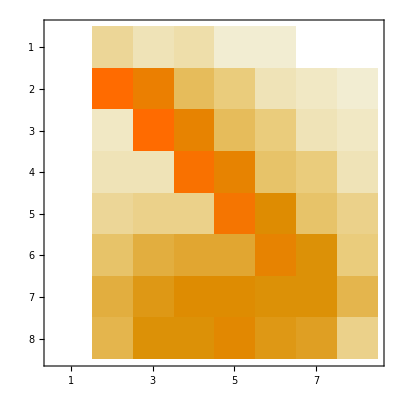
{(0 | 7 | 4 | 5 | 2 | 2 | 0 | 0
0 | 29 | 22 | 12 | 9 | 4 | 3 | 2
0 | 3 | 29 | 21 | 12 | 9 | 4 | 3
0 | 4 | 4 | 27 | 21 | 11 | 9 | 4
0 | 7 | 8 | 8 | 26 | 19 | 11 | 8
0 | 11 | 14 | 15 | 15 | 21 | 18 | 9
0 | 14 | 17 | 19 | 19 | 18 | 18 | 13
0 | 13 | 18 | 18 | 20 | 17 | 16 | 8),-Graphics-}

```mathematica
(* lengths of coefficients in the equations.
rows are variables, columns are equations.
may be helpful? *)
{MatrixForm[#],MatrixPlot[#]}&[Map[Length,
{Coefficient[#[[2]],a]&/@sys,
Coefficient[#[[2]],b]&/@sys,
Coefficient[#[[2]],c]&/@sys,
Coefficient[#[[2]],d]&/@sys,
Coefficient[#[[2]],e]&/@sys,
Coefficient[#[[2]],k]&/@sys,
Coefficient[#[[2]],g]&/@sys,
Coefficient[#[[2]],h]&/@sys},{2}]]
```

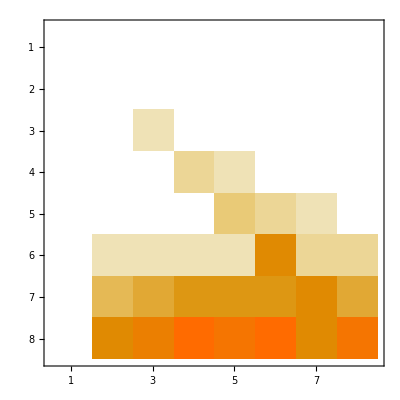
{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 3 | 2 | 0
0 | 2 | 2 | 2 | 2 | 8 | 3 | 3
0 | 5 | 6 | 7 | 7 | 7 | 8 | 6
0 | 8 | 9 | 11 | 10 | 11 | 8 | 10),-Graphics-}

```mathematica
{MatrixForm[#],MatrixPlot[#]}&[Map[Length,
{Coefficient[#[[2]],a,2]&/@sys,
Coefficient[#[[2]],b,2]&/@sys,
Coefficient[#[[2]],c,2]&/@sys,
Coefficient[#[[2]],d,2]&/@sys,
Coefficient[#[[2]],e,2]&/@sys,
Coefficient[#[[2]],k,2]&/@sys,
Coefficient[#[[2]],g,2]&/@sys,
Coefficient[#[[2]],h,2]&/@sys},{2}]]
```